# xPand Minimal Example

## Set up

```mathematica
SetDirectory["~/CMB"];
```

```mathematica
Block[{Print},
<<xPand/xPand.m;
]
$DefInfoQ=False;
SetOptions[AutomaticRules,Verbose->False];
```

We define the manifold, the metric and the slicing

```mathematica
(*DefConstantSymbol[d];*)
DefManifold[M,4(*d*),{α,β,γ,μ,ν,λ,σ}];
DefMetric[-1,g[-α,-β],CD,{";","OverBar[∇]"},PrintAs->"ḡ"];
BackgroundSlicing[hM,n,g,cdM,{"|","D̄"},Minkowski];
BackgroundSlicing[h,n,g,cd,{"|","D̄"},FLFlat];
BackgroundSlicing[h2,n2,g,cd2,{"|","D̄"},FLCurved];
BackgroundSlicing[h3,n3,g,cd3,{"|","D̄"},BianchiI];
BackgroundSlicing[h4,n4,g,cd4,{"|","D̄"},BianchiB];
```

** DefMetric: Don't know yet how to define epsilon for a frozen metric.

** MakeRule: Potential problems moving indices on the LHS.

** DefMetric: Don't know yet how to define epsilon for a frozen metric.

** MakeRule: Potential problems moving indices on the LHS.

** DefMetric: Don't know yet how to define epsilon for a frozen metric.

** MakeRule: Potential problems moving indices on the LHS.

** DefMetric: Don't know yet how to define epsilon for a frozen metric.

** MakeRule: Potential problems moving indices on the LHS.

These commands are necessary, but if they are forgotten, they are automatically called. So for a minimal example we do not evaluate them

```mathematica
DefMetricFields[g,dg,hM]
DefMatterFields[uf, duf,hM]

DefMetricFields[g,dg,h]
DefMatterFields[uf, duf,h]

DefMetricFields[g,dg,h2]
DefMatterFields[uf, duf,h2]
DefMetricFields[g,dg,h3]
DefMatterFields[uf, duf,h3]

DefMetricFields[g,dg,h4]
DefMatterFields[uf, duf,h4]
```

The Hubble factor  has to be introduced from the scale factor.

#### Benchmark

```mathematica
MyxPandBenchMark[expr_,h_,order_,gauge_]:=ToxPand[expr,dg,uf,duf,h, gauge, order]
```

```mathematica
$DebugInfoQ=False;
ordermax=4
```

4

```mathematica
(*AbsoluteTiming@MyxPandBenchMark[RicciScalarCD[],h4,2,NewtonGauge]
AbsoluteTiming@MyxPandBenchMark[RicciScalarCD[],h4,2,AnyGauge]*)
```

```mathematica
TimingsxPert=Table[{i,First@AbsoluteTiming[ExpandPerturbation@Perturbed[Conformal[g,gah42][RicciScalarCD[]],i]//ContractMetric//ToCanonical]},{i,1,ordermax}]
```

$Aborted

```mathematica
TimingsMinkowski=Table[{i,First@AbsoluteTiming[MyxPandBenchMark[RicciScalarCD[],hM,i,NewtonGauge]]},{i,1,ordermax}]
TimingsMinkowskiAny=Table[{i,First@AbsoluteTiming[MyxPandBenchMark[RicciScalarCD[],hM,i,AnyGauge]]},{i,1,ordermax}]
```

{{1,1.26763},{2,8.368549},{3,68.194944}}

{{1,1.54097},{2,18.53417},{3,221.87911}}

```mathematica
TimingsFLFlat=Table[{i,First@AbsoluteTiming[MyxPandBenchMark[RicciScalarCD[],h,i,NewtonGauge]]},{i,1,ordermax}]
TimingsFLFlatAny=Table[{i,First@AbsoluteTiming[MyxPandBenchMark[RicciScalarCD[],h,i,AnyGauge]]},{i,1,ordermax}]
```

{{1,1.85443},{2,12.47621},{3,129.57547}}

{{1,2.30938},{2,26.79738},{3,335.37679}}

```mathematica
TimingsFLCurved=Table[{i,First@AbsoluteTiming[MyxPandBenchMark[RicciScalarCD[],h2,i,NewtonGauge]]},{i,1,ordermax}]
TimingsFLCurvedAny=Table[{i,First@AbsoluteTiming[MyxPandBenchMark[RicciScalarCD[],h2,i,AnyGauge]]},{i,1,ordermax}]
```

{{1,1.94716},{2,13.55533},{3,141.72019}}

{{1,2.64258},{2,33.97226},{3,466.289503}}

```mathematica
TimingsBianchiI=Table[{i,First@AbsoluteTiming[MyxPandBenchMark[RicciScalarCD[],h3,i,NewtonGauge]]},{i,1,ordermax}]
TimingsBianchiIAny=Table[{i,First@AbsoluteTiming[MyxPandBenchMark[RicciScalarCD[],h3,i,AnyGauge]]},{i,1,ordermax}]
```

{{1,5.884028},{2,43.954261},{3,886.281212}}

{{1,6.516881},{2,82.90651},{3,12837.29855}}

```mathematica
TimingsBianchiB=Table[{i,First@AbsoluteTiming[MyxPandBenchMark[RicciScalarCD[],h4,i,NewtonGauge]]},{i,1,ordermax-1}]
TimingsBianchiBAny=Table[{i,First@AbsoluteTiming[MyxPandBenchMark[RicciScalarCD[],h4,i,AnyGauge]]},{i,1,ordermax-1}]
```

{{1,12.23886},{2,106.2978}}

Just to have an idea of the ratio of timings between succesive orders. We clearly see that it is an approximate power law.

```mathematica
FirstTime=True
```

False

```mathematica
NameFileNewt=StringJoin["SaveTimingsNewtonGauge",ToString[ordermax],".dat"];
If[FirstTime,
Put[{TimingsxPert,TimingsMinkowski,TimingsFLFlat,TimingsFLCurved,TimingsBianchiI,TimingsBianchiB},NameFileNewt];,{TimingsxPert,TimingsMinkowski,TimingsFLFlat,TimingsFLCurved,TimingsBianchiI,TimingsBianchiB}=Get[NameFileNewt]]
```

{{{1,0.18275},{2,0.550151},{3,2.5043},{4,14.2825}},{{1,1.28671},{2,8.216333},{3,77.654352},{4,2024.18814}},{{1,2.02813},{2,13.37317},{3,156.21212},{4,4456.848306}},{{1,2.18694},{2,14.64508},{3,181.28403},{4,4867.564838}},{{1,5.703992},{2,51.155764},{3,1224.86295},{4,38843.792745}},{{1,14.03925},{2,122.18303},{3,2554.99163}}}

```mathematica
NameFileAny=StringJoin["SaveTimingsAnyGauge",ToString[ordermax],".dat"];
If[FirstTime,
Put[{TimingsxPert,TimingsMinkowskiAny,TimingsFLFlatAny,TimingsFLCurvedAny,TimingsBianchiIAny,TimingsBianchiBAny},NameFileAny];,{TimingsxPert,TimingsMinkowskiAny,TimingsFLFlatAny,TimingsFLCurvedAny,TimingsBianchiIAny,TimingsBianchiBAny}=Get[NameFileAny]]
```

{{{1,0.18275},{2,0.550151},{3,2.5043},{4,14.2825}},{{1,1.57549},{2,18.10678},{3,232.70759},{4,4757.05312}},{{1,2.60921},{2,28.75592},{3,381.127202},{4,7951.476269}},{{1,3.05414},{2,37.475055},{3,517.402143},{4,9905.432302}},{{1,7.855177},{2,90.912973},{3,1953.50485},{4,52169.753148}}}

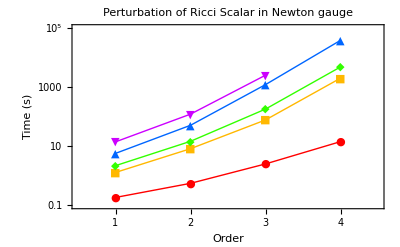

```mathematica
plotnewt=ListLogPlot[{TimingsxPert,TimingsMinkowski,(*TimingsFLFlat,*)TimingsFLCurved,TimingsBianchiI,TimingsBianchiB},Frame->True,FrameLabel->{Style["Order",12],Style["Time (s)",12]},PlotRange->{{0.5,4.5},{.1,100000}},PlotLabel->Style["Perturbation of Ricci Scalar in Newton gauge",12],PlotMarkers->{Automatic,Medium},FrameStyle->{{Thickness[.0035],Thickness[.0035]},{Thickness[.0035],Thickness[.0035]}},Joined->True,PlotStyle->{Hue[0],Hue[0.12],Hue[0.3],Hue[0.6],Hue[0.8],Hue[0.9]}]
```

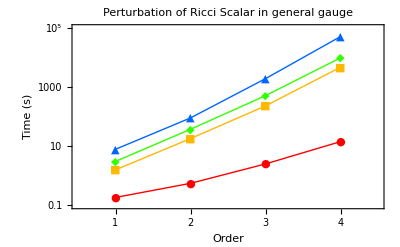

```mathematica
plotany=ListLogPlot[{TimingsxPert,TimingsMinkowskiAny,(*TimingsFLFlatAny,*)TimingsFLCurvedAny,TimingsBianchiIAny,TimingsBianchiBAny},Frame->True,FrameLabel->{Style["Order",12],Style["Time (s)",12]},PlotRange->{{0.5,4.5},{.1,100000}},PlotLabel->Style["Perturbation of Ricci Scalar in general gauge",12],PlotMarkers->{Automatic,Medium},FrameStyle->{{Thickness[.0035],Thickness[.0035]},{Thickness[.0035],Thickness[.0035]}},Joined->True,PlotStyle->{Hue[0],Hue[0.12],Hue[0.3],Hue[0.6],Hue[0.8]}]
```

```mathematica
Export["TimingNewtonGauge.pdf",plotnewt,"pdf"];
Export["TimingNewtonGauge.eps",plotnewt,"eps"];
```

```mathematica
Export["TimingAnyGauge.pdf",plotany,"pdf"];
Export["TimingAnyGauge.eps",plotany,"eps"];
```